```mathematica
pos[x_]:=If[x>0,x,0];
f[x_,y_]=-x+pos[-3/4y-1/2+1];
g[x_,y_]=-y+pos[-3/4x-1/2+1];
h[x_,y_]=+1/2+pos[-3/4x-3/2y+1];
```

```mathematica
pos[-1]
```

0

```mathematica
Plot3D[{eq1,0},{x,0,5/7}, {y,0,5/7}]
```

-Graphics3D-

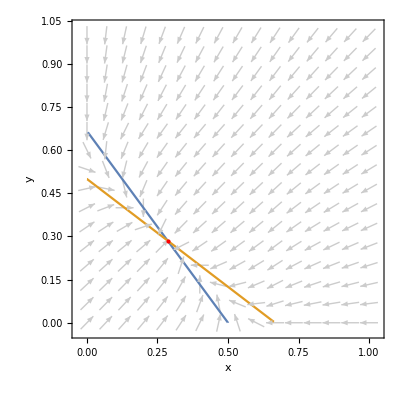

```mathematica
min=0;max=1;vp=VectorPlot[{f[x,y],g[x,y]},{x,min,max},{y,min,max},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,min,max},{y,min,max}];
ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}];
Show[vp,cp,Graphics[{Red,PointSize[Large],Point[{x,y}]/.ptRules}]]
```

```mathematica
pos[x_]:=If[x>0,x,0];
f[x_,y_,z_]=-x+pos[-3/4y-3/2z+1];
g[x_,y_,z_]=-y+pos[-3/4x-3/2z+1];
h[x_,y_,z_]=-z+pos[-3/4x-3/2y+1];
```

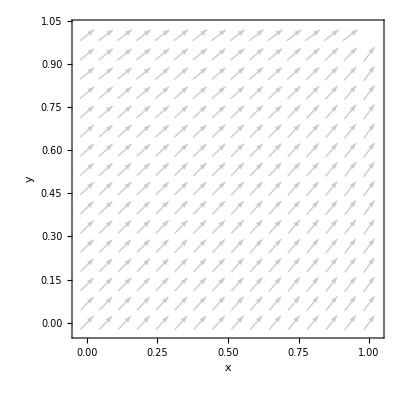

```mathematica
vp=VectorPlot[{f[x,y,-1/2],g[x,y,-1/2]},{x,0,max},{y,0,max},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
Show[vp,Graphics[{Red,PointSize[Large]}]]
```

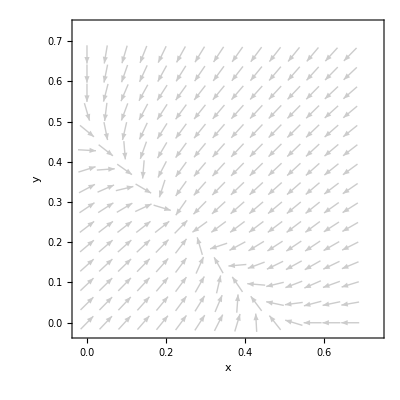

```mathematica
min=0;max=5/7;vp=VectorPlot[{f[x,y,5/13],g[x,y,5/13]},{x,min,max},{y,min,max},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
Show[vp,Graphics[{Red,PointSize[Large]}]]
```

```mathematica
min=3/13;max=4.1/7;
vp=SliceVectorPlot3D[{f[x,y,z],g[x,y,z],h[x,y,z]},{x==max,z==5/13},{x,min,max},{y,min,max},{z,-.002,5/13},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->15,VectorStyle->{GrayLevel[0.8]}];
Show[vp]
```

-Graphics3D-

```mathematica
Plot3D[{f[0,y,z],0},{y,0,5/7}, {z,-1/2,5/13}]
```

-Graphics3D-

```mathematica
Plot3D[Reduce[f[5/7,y,z]>0,{y,z}],{y,0,5/7},{z,-1/2,5/13}]
```

Reduce::ivar: 0.0000510714 is not a valid variable.

Reduce::ivar: 0.0510715 is not a valid variable.

Reduce::ivar: 0.102092 is not a valid variable.

General::stop: Further output of Reduce::ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
5/13*3/2
```

15/26

```mathematica
-(3/4*5/7+3/2*5/13)+1
```

-41/364

```mathematica
-3/4*5/7+1-3/2*5/13
```

-41/364

```mathematica
3/2*1/2
```

3/4

```mathematica
Reduce[g[0,5/7,z]>0,{z}]
```

If[1-(3 z)/2>0,1-(3 0)/4-(3 z)/2,0]∈ℝ&&z<4/21

```mathematica
-5/13
```

-5/13

```mathematica
B=Reduce[h[0,y,5/13]>0,{y,z}, Reals]
```

y<16/39

```mathematica
A=Reduce[f[5/7,y,z]>0,{y,z},Reals]
```

z<1/42 (8-21 y)

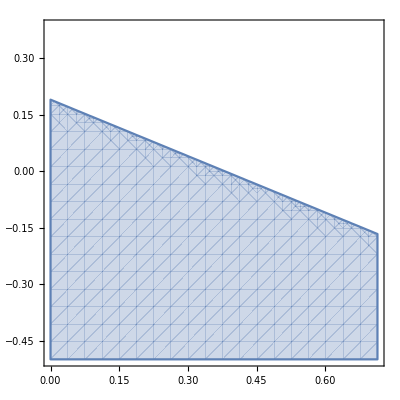

```mathematica
RegionPlot[z<1/42 (8-21 y),{y,0,5/7},{z,-1/2,5/13}]
```

```mathematica
A&&B
```

z<1/42 (8-21 y)&&y<16/39

```mathematica
For[i=1,i<3,i++,Print[x[i]==0]]
```

x[1]==0

x[2]==0

```mathematica
x_o
```

x_o

```mathematica
eqs={f,g,h}
```

{f,g,h}

```mathematica
eqs[[1]]
```

f

```mathematica
calcN0[eqs_,ranges_]:=ndim=Length[eqs],For[i=1,ndim,i++,For[j=1,2,j++,Reduce[eqs[[i]][ranges[[j]],x[2],x[3]]>0,Reals]]];
```

```mathematica
Plot[(x:Blank[1])==0,{x_1,0,1}]
```

Plot::itraw: Raw object x_ cannot be used as an iterator.

Plot[(x:Blank[1])==0,{x_ 1,0,1}]

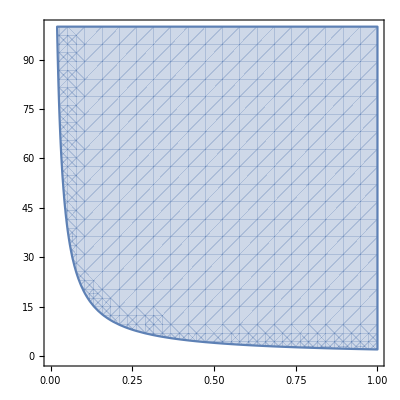

```mathematica
RegionPlot[x[1]x[2]>2,{x[1],0,1},{x[2],-1,100}]
```

```mathematica
Reduce[eqs[[1]][0,x[2],x[3]]>0,Reals]
```

x[2]<1/3 (4-6 x[3])

```mathematica
Reduce[eqs[[1]][0,x[2],x[3]]>0,Reals]
```

x[2]<1/3 (4-6 x[3])

```mathematica
Apply[f,Table[If[i==2,0,x[i]],{i,3}]]
```

If[1-(3 x[3])/2>0,1-(3 0)/4-(3 x[3])/2,0]-x[1]

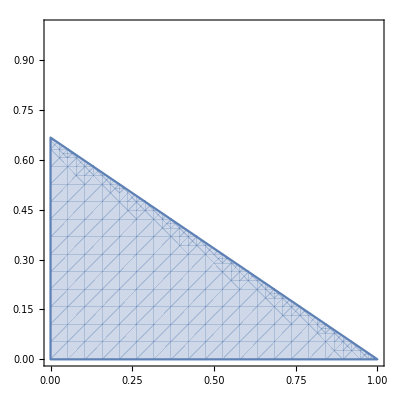

```mathematica
RegionPlot[Reduce[Apply[f,Table[If[i==2,0,x[i]],{i,3}]]>0,Reals],{x[1],0,1},{x[3],0,1}]
```

```mathematica
RegionPlot3D[Reduce[Apply[f,Table[If[i==2,0,x[i]],{i,3}]]>0,Reals]&&(x[2]==0),{x[1],0,1},{x[2],0,1},{x[3],0,1}]
```

-Graphics3D-

```mathematica
ranges={{0,5/7},{0,5/7},{-1/2,5/13}}
```

{{0,5/7},{0,5/7},{-1/2,5/13}}

```mathematica
X[[1]][[1]] = 0
```

Set::noval: Symbol X in part assignment does not have an immediate value.

0

```mathematica
Xminint=Reduce[Apply[eqs[[1]],Table[If[i==1,ranges[[1]][[1]],x[i]],{i,3}]]<0,Reals]&&(x[1]==ranges[[1]][[1]])
```

False

```mathematica
Xmin1=Reduce[Apply[eqs[[1]],Table[If[i==1,ranges[[1]][[1]],x[i]],{i,3}]]<0,Reals]&&(x[1]==ranges[[1]][[1]])
```